```mathematica
(*Import danych z pliku CSV*)covidData = Import["https://github.com/CSSEGISandData/COVID-19/raw/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
```

```mathematica
Dimensions[covidData]
```

{290,1147}

```mathematica
polandCases =Cases[covidData , {_,"Poland" , __}][[1,5;;]];
```

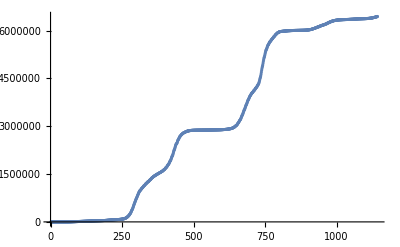

```mathematica
ListPlot[polandCases]
```

```mathematica
dailyCases=Rest[polandCases]-Most[polandCases];
```

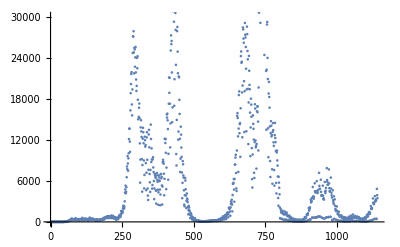

```mathematica
ListPlot[dailyCases]
```

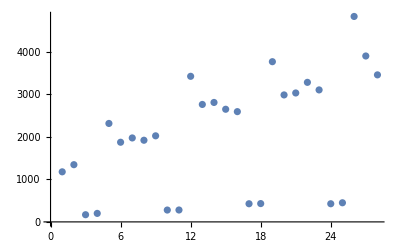

```mathematica
last4weeks = Take[dailyCases,-28];
ListPlot[last4weeks]
```